```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/Top-FormFactors-FA/Top-FormFactors-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g-g- t- t (1-loop)

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT = {V[4],V[4]}-> {F[9],-F[9]} ;
allDiags = InsertFields[tops0,processGGT, InsertionLevel-> {Particles},GenericModel->"../../Models/Top-FormFactors-FA/Top-FormFactors-FA_FC",ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

generic model {../../Models/Top-FormFactors-FA/Top-FormFactors-FA_FC} initialized

classes model {../../Models/Top-FormFactors-FA/Top-FormFactors-FA} initialized

in total: 4 Particles insertions

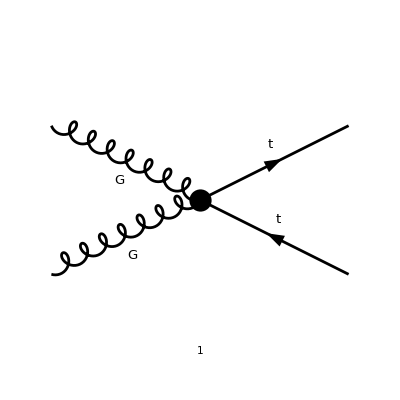

```mathematica
goodDiags=DiagramExtract[allDiags,{1}]; 
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 300,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p3,p4},LorentzIndexNames->{μ,ν},OutgoingMomenta->{-p2,-p1},LoopMomenta->{q},SUNIndexNames->{cc3,cc4,aa,bb},SUNFIndexNames->{a,b,c2,c1},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[DiracSimplify[FCReplaceMomenta[SUNSimplify[DiracSimplify[ampA]],{p4-> -p1-p2-p3}]]]
```

in total: 1 Particles amplitude

-ⅈ π^2 gs^2 itri yDM^2 ((T^cc4 T^cc3)_c2c1 ((C1+2 C11) g^μν (γ·p1).(γ̄)^6-(C1+2 C12) g^μν (γ·p2).(γ̄)^6+(C1+2 C12) p3^ν γ^μ.(γ̄)^6+2 C1 p1^μ γ^ν.(γ̄)^6+C1 p1^ν γ^μ.(γ̄)^6-C1 p2^ν γ^μ.(γ̄)^6+C1 p3^μ γ^ν.(γ̄)^6+2 C11 g^μν (γ·p3).(γ̄)^6+2 C11 p1^ν γ^μ.(γ̄)^6-2 C11 p2^μ γ^ν.(γ̄)^6-2 C12 g^μν (γ·p3).(γ̄)^6+4 C12 p1^μ γ^ν.(γ̄)^6+2 C12 p2^μ γ^ν.(γ̄)^6-2 C12 p2^ν γ^μ.(γ̄)^6+2 C12 p3^μ γ^ν.(γ̄)^6)-(T^cc3 T^cc4)_c2c1 ((C1+2 C11) g^μν (γ·p2).(γ̄)^6-(C1+2 C12) g^μν (γ·p1).(γ̄)^6+(C1+2 C12) p3^ν γ^μ.(γ̄)^6-C1 p1^ν γ^μ.(γ̄)^6+2 C1 p2^μ γ^ν.(γ̄)^6+C1 p2^ν γ^μ.(γ̄)^6+C1 p3^μ γ^ν.(γ̄)^6+2 C11 g^μν (γ·p3).(γ̄)^6-2 C11 p1^μ γ^ν.(γ̄)^6+2 C11 p2^ν γ^μ.(γ̄)^6-2 C12 g^μν (γ·p3).(γ̄)^6+2 C12 p1^μ γ^ν.(γ̄)^6-2 C12 p1^ν γ^μ.(γ̄)^6+4 C12 p2^μ γ^ν.(γ̄)^6+2 C12 p3^μ γ^ν.(γ̄)^6))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify);
```

```mathematica
ampEsimp=ExpandScalarProduct[DiracSimplify[ampC/.{DiracGamma[7]->1-DiracGamma[6]}]];
```

```mathematica
ampEsimp3=FullSimplify[DiracSimplify[ampEsimp/.{itri->1}]]
```

-ⅈ π^2 gs^2 yDM^2 ((T^cc4 T^cc3)_c2c1 ((C1+2 C11) g^μν (γ·p1).(γ̄)^6-(C1+2 C12) g^μν (γ·p2).(γ̄)^6+(C1+2 C12) p3^ν γ^μ.(γ̄)^6+2 C1 p1^μ γ^ν.(γ̄)^6+C1 p1^ν γ^μ.(γ̄)^6-C1 p2^ν γ^μ.(γ̄)^6+C1 p3^μ γ^ν.(γ̄)^6+2 C11 g^μν (γ·p3).(γ̄)^6+2 C11 p1^ν γ^μ.(γ̄)^6-2 C11 p2^μ γ^ν.(γ̄)^6-2 C12 g^μν (γ·p3).(γ̄)^6+4 C12 p1^μ γ^ν.(γ̄)^6+2 C12 p2^μ γ^ν.(γ̄)^6-2 C12 p2^ν γ^μ.(γ̄)^6+2 C12 p3^μ γ^ν.(γ̄)^6)-(T^cc3 T^cc4)_c2c1 ((C1+2 C11) g^μν (γ·p2).(γ̄)^6-(C1+2 C12) g^μν (γ·p1).(γ̄)^6+(C1+2 C12) p3^ν γ^μ.(γ̄)^6-C1 p1^ν γ^μ.(γ̄)^6+2 C1 p2^μ γ^ν.(γ̄)^6+C1 p2^ν γ^μ.(γ̄)^6+C1 p3^μ γ^ν.(γ̄)^6+2 C11 g^μν (γ·p3).(γ̄)^6-2 C11 p1^μ γ^ν.(γ̄)^6+2 C11 p2^ν γ^μ.(γ̄)^6-2 C12 g^μν (γ·p3).(γ̄)^6+2 C12 p1^μ γ^ν.(γ̄)^6-2 C12 p1^ν γ^μ.(γ̄)^6+4 C12 p2^μ γ^ν.(γ̄)^6+2 C12 p3^μ γ^ν.(γ̄)^6))

```mathematica
Collect[ampEsimp3/(I Pi^2 gs^2 yDM^2),{C1,C11,C12,SUNTF[{SUNIndex[cc3],SUNIndex[cc4]},SUNFIndex[c2],SUNFIndex[c1]],SUNTF[{SUNIndex[cc4],SUNIndex[cc3]},SUNFIndex[c2],SUNFIndex[c1]]},FullSimplify]
```

C1 ((T^cc3 T^cc4)_c2c1 (g^μν ((γ·p2).(γ̄)^6-(γ·p1).(γ̄)^6)+γ^μ.(γ̄)^6 (-p1^ν+p2^ν+p3^ν)+γ^ν.(γ̄)^6 (2 p2^μ+p3^μ))+(T^cc4 T^cc3)_c2c1 (g^μν ((γ·p2).(γ̄)^6-(γ·p1).(γ̄)^6)-γ^μ.(γ̄)^6 (p1^ν-p2^ν+p3^ν)-γ^ν.(γ̄)^6 (2 p1^μ+p3^μ)))+C11 (2 (T^cc3 T^cc4)_c2c1 (g^μν ((γ·p2).(γ̄)^6+(γ·p3).(γ̄)^6)-p1^μ γ^ν.(γ̄)^6+p2^ν γ^μ.(γ̄)^6)-2 (T^cc4 T^cc3)_c2c1 (g^μν ((γ·p1).(γ̄)^6+(γ·p3).(γ̄)^6)+p1^ν γ^μ.(γ̄)^6-p2^μ γ^ν.(γ̄)^6))+C12 (2 (T^cc3 T^cc4)_c2c1 (g^μν (-((γ·p1).(γ̄)^6+(γ·p3).(γ̄)^6))+γ^ν.(γ̄)^6 (p1^μ+2 p2^μ+p3^μ)+γ^μ.(γ̄)^6 (p3^ν-p1^ν))+2 (T^cc4 T^cc3)_c2c1 (g^μν ((γ·p2).(γ̄)^6+(γ·p3).(γ̄)^6)-γ^ν.(γ̄)^6 (2 p1^μ+p2^μ+p3^μ)+γ^μ.(γ̄)^6 (p2^ν-p3^ν)))

```mathematica
spinorChains2=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___],All]][[All,1]];
allTerms=Sort[spinorChains2]
pairs1=Cases2[ampEsimp3,Pair];
allPairs=Join[pairs1,{}]
su3prods=Join[Cases2[ampEsimp3,SUNTF],Cases2[ampEsimp3,SUNF]]
```

{γ^μ.(γ̄)^6,γ^ν.(γ̄)^6,(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6,(γ·p3).(γ̄)^6}

{g^μν,p1^μ,p2^μ,p3^μ,p1^ν,p2^ν,p3^ν}

{(T^cc3 T^cc4)_c2c1,(T^cc4 T^cc3)_c2c1}

## Coefficients for each term

```mathematica
su3Terms={};
Do[c=FullSimplify[Coefficient[Coefficient[Coefficient[Expand[ampEsimp3],su3prods[[i]]],allTerms[[j]]],allPairs[[k]]]];
If[c==0,Continue[]];
c= Simplify[c/(I Pi^2 gs^2 yDM^2)];
AppendTo[su3Terms,{su3prods[[i]],allTerms[[j]],allPairs[[k]],c}];
,{i,1,Length[su3prods]},{j,1,Length[allTerms]},{k,1,Length[allPairs]}];
```

#### Check that all terms have been correctly split

```mathematica
ampTot = I Pi^2 gs^2 yDM^2 Sum[su3Terms[[i,1]] su3Terms[[i,2]] su3Terms[[i,3]]su3Terms[[i,4]],{i,1,Length[su3Terms]}];
Simplify[ampTot-ampEsimp3]
```

0

```mathematica
su3Terms
```

((T^cc3 T^cc4)_c2c1 | γ^μ.(γ̄)^6 | p1^ν | -C1-2 C12
(T^cc3 T^cc4)_c2c1 | γ^μ.(γ̄)^6 | p2^ν | C1+2 C11
(T^cc3 T^cc4)_c2c1 | γ^μ.(γ̄)^6 | p3^ν | C1+2 C12
(T^cc3 T^cc4)_c2c1 | γ^ν.(γ̄)^6 | p1^μ | 2 C12-2 C11
(T^cc3 T^cc4)_c2c1 | γ^ν.(γ̄)^6 | p2^μ | 2 (C1+2 C12)
(T^cc3 T^cc4)_c2c1 | γ^ν.(γ̄)^6 | p3^μ | C1+2 C12
(T^cc3 T^cc4)_c2c1 | (γ·p1).(γ̄)^6 | g^μν | -C1-2 C12
(T^cc3 T^cc4)_c2c1 | (γ·p2).(γ̄)^6 | g^μν | C1+2 C11
(T^cc3 T^cc4)_c2c1 | (γ·p3).(γ̄)^6 | g^μν | 2 (C11-C12)
(T^cc4 T^cc3)_c2c1 | γ^μ.(γ̄)^6 | p1^ν | -C1-2 C11
(T^cc4 T^cc3)_c2c1 | γ^μ.(γ̄)^6 | p2^ν | C1+2 C12
(T^cc4 T^cc3)_c2c1 | γ^μ.(γ̄)^6 | p3^ν | -C1-2 C12
(T^cc4 T^cc3)_c2c1 | γ^ν.(γ̄)^6 | p1^μ | -2 (C1+2 C12)
(T^cc4 T^cc3)_c2c1 | γ^ν.(γ̄)^6 | p2^μ | 2 (C11-C12)
(T^cc4 T^cc3)_c2c1 | γ^ν.(γ̄)^6 | p3^μ | -C1-2 C12
(T^cc4 T^cc3)_c2c1 | (γ·p1).(γ̄)^6 | g^μν | -C1-2 C11
(T^cc4 T^cc3)_c2c1 | (γ·p2).(γ̄)^6 | g^μν | C1+2 C12
(T^cc4 T^cc3)_c2c1 | (γ·p3).(γ̄)^6 | g^μν | 2 C12-2 C11)

## UFO Result from FeynRules

```mathematica
FFVV1="P(4,3)*Gamma(3,2,-1)*ProjP(-1,1) - P(3,4)*Gamma(4,2,-1)*ProjP(-1,1)";
FFVV3="P(-1,1)*Gamma(-1,2,-2)*Metric(3,4)*ProjP(-2,1) - P(-1,2)*Gamma(-1,2,-2)*Metric(3,4)*ProjP(-2,1) + P(4,1)*Gamma(3,2,-1)*ProjP(-1,1) - P(4,2)*Gamma(3,2,-1)*ProjP(-1,1) + P(4,3)*Gamma(3,2,-1)*ProjP(-1,1) + P(3,1)*Gamma(4,2,-1)*ProjP(-1,1) - P(3,2)*Gamma(4,2,-1)*ProjP(-1,1) - P(3,4)*Gamma(4,2,-1)*ProjP(-1,1)";
FFVV4="P(-1,1)*Gamma(-1,2,-2)*Metric(3,4)*ProjP(-2,1) - P(-1,2)*Gamma(-1,2,-2)*Metric(3,4)*ProjP(-2,1) + P(4,1)*Gamma(3,2,-1)*ProjP(-1,1) - P(4,2)*Gamma(3,2,-1)*ProjP(-1,1) - P(4,3)*Gamma(3,2,-1)*ProjP(-1,1) + P(3,1)*Gamma(4,2,-1)*ProjP(-1,1) - P(3,2)*Gamma(4,2,-1)*ProjP(-1,1) + P(3,4)*Gamma(4,2,-1)*ProjP(-1,1)";
FFVV5="-(P(-1,3)*Gamma(-1,2,-2)*Metric(3,4)*ProjP(-2,1))/4. + (P(-1,4)*Gamma(-1,2,-2)*Metric(3,4)*ProjP(-2,1))/4. + P(4,3)*Gamma(3,2,-1)*ProjP(-1,1) + (P(4,4)*Gamma(3,2,-1)*ProjP(-1,1))/4. - (P(3,3)*Gamma(4,2,-1)*ProjP(-1,1))/4. - P(3,4)*Gamma(4,2,-1)*ProjP(-1,1)";
FFVV6="-(P(-1,3)*Gamma(-1,2,-2)*Metric(3,4)*ProjP(-2,1)) + P(-1,4)*Gamma(-1,2,-2)*Metric(3,4)*ProjP(-2,1) + P(4,4)*Gamma(3,2,-1)*ProjP(-1,1) - P(3,3)*Gamma(4,2,-1)*ProjP(-1,1)";
```

#### Functions to convert from UFO to FeynCalc

```mathematica
P[a_,b_]:=Which[a>0,FVD[ToExpression[StringJoin["p",ToString[b]]],a],a==-1,FVD[ToExpression[StringJoin["p",ToString[b]]],aa],a==-2,FVD[ToExpression[StringJoin["p",ToString[b]]],bb]]/.{3->μ,4->ν};
GAMMA[a_,b_,c_]:= Which[a==3,GAD[μ],a==4,GAD[ν],a==-1,GAD[aa],a==-2,GAD[bb]];
Metric[a_,b_]:=MTD[a,b]/.{3->μ,4->ν};
ProjP[a_,b_]:= 1;
ProjM[a_,b_]:= GAD[7];
Convert[expr_]:=(ToExpression[StringReplace[expr,{"Gamma"->"GAMMA","/4."->"/4"}],TraditionalForm]/.{GAD[aa] FVD[a_,aa]:>  GSD[a],GAD[bb] FVD[a_,bb]:>  GSD[a]}).GA[6]
```

```mathematica
FFVV1expr=DiracSimplify[Convert[FFVV1]]
FFVV3expr=DiracSimplify[Convert[FFVV3]]
FFVV4expr=DiracSimplify[Convert[FFVV4]]
FFVV5expr=DiracSimplify[Convert[FFVV5]]
FFVV6expr=DiracSimplify[Convert[FFVV6]]
```

p3^ν γ^μ.(γ̄)^6-p4^μ γ^ν.(γ̄)^6

g^μν (γ·p1).(γ̄)^6-g^μν (γ·p2).(γ̄)^6+p1^μ γ^ν.(γ̄)^6+p1^ν γ^μ.(γ̄)^6-p2^μ γ^ν.(γ̄)^6-p2^ν γ^μ.(γ̄)^6+p3^ν γ^μ.(γ̄)^6-p4^μ γ^ν.(γ̄)^6

g^μν (γ·p1).(γ̄)^6-g^μν (γ·p2).(γ̄)^6+p1^μ γ^ν.(γ̄)^6+p1^ν γ^μ.(γ̄)^6-p2^μ γ^ν.(γ̄)^6-p2^ν γ^μ.(γ̄)^6-p3^ν γ^μ.(γ̄)^6+p4^μ γ^ν.(γ̄)^6

-1/4 g^μν (γ·p3).(γ̄)^6+1/4 g^μν (γ·p4).(γ̄)^6-1/4 p3^μ γ^ν.(γ̄)^6+p3^ν γ^μ.(γ̄)^6-p4^μ γ^ν.(γ̄)^6+1/4 p4^ν γ^μ.(γ̄)^6

g^μν (-(γ·p3).(γ̄)^6)+g^μν (γ·p4).(γ̄)^6-p3^μ γ^ν.(γ̄)^6+p4^ν γ^μ.(γ̄)^6

```mathematica
color={SUNF[a,cc3,cc4]SUNTF[{SUNIndex[a]},SUNFIndex[c2],SUNFIndex[c1]],SUNTF[{SUNIndex[cc4],SUNIndex[cc3]},SUNFIndex[c2],SUNFIndex[c1]],SUNTF[{SUNIndex[cc3],SUNIndex[cc4]},SUNFIndex[c2],SUNFIndex[c1]]}
```

{T_c2c1^a f^acc3cc4,(T^cc4 T^cc3)_c2c1,(T^cc3 T^cc4)_c2c1}

```mathematica
GC69=-2*C1*Pi^2*gs^2yDM^2;
GC70=C11*Pi^2*gs^2yDM^2;
GC71=-4*C12*Pi^2*gs^2yDM^2;
GC78=-I (C1*Pi^2*gs^2yDM^2)-I C11*Pi^2*gs^2yDM^2-I C12*Pi^2*gs^2yDM^2;
couplings={{GC69,0,0,GC71,GC70},{0,0,GC78,0,0},{0,GC78,0,0,0}};
LFFVV={FFVV1expr,FFVV3expr,FFVV4expr,FFVV5expr,FFVV6expr};
```

```mathematica
ttGG = Total[Table[couplings[[i,j]] color[[i]] LFFVV[[j]],{i,1,3},{j,1,5}],2];
```

```mathematica
ttGGsimp=Simplify[ttGG/.{SUNF[a,cc3,cc4]SUNTF[{SUNIndex[a]},SUNFIndex[c2],SUNFIndex[c1]]-> I (SUNTF[{SUNIndex[cc4],SUNIndex[cc3]},SUNFIndex[c2],SUNFIndex[c1]]-SUNTF[{SUNIndex[cc3],SUNIndex[cc4]},SUNFIndex[c2],SUNFIndex[c1]])}];
ttGGsimp2=Simplify[FCReplaceMomenta[ttGGsimp,{p4->-p1-p2-p3}]];
ttGGsimp3=FullSimplify[DiracSimplify[ttGGsimp2]];
```

```mathematica
x=Collect[ampEsimp3/(I Pi^2 gs^2 yDM^2),{C1,C11,C12,SUNTF[{SUNIndex[cc3],SUNIndex[cc4]},SUNFIndex[c2],SUNFIndex[c1]],SUNTF[{SUNIndex[cc4],SUNIndex[cc3]},SUNFIndex[c2],SUNFIndex[c1]]},FullSimplify]
```

C1 ((T^cc3 T^cc4)_c2c1 (g^μν ((γ·p2).(γ̄)^6-(γ·p1).(γ̄)^6)+γ^μ.(γ̄)^6 (-p1^ν+p2^ν+p3^ν)+γ^ν.(γ̄)^6 (2 p2^μ+p3^μ))+(T^cc4 T^cc3)_c2c1 (g^μν ((γ·p2).(γ̄)^6-(γ·p1).(γ̄)^6)-γ^μ.(γ̄)^6 (p1^ν-p2^ν+p3^ν)-γ^ν.(γ̄)^6 (2 p1^μ+p3^μ)))+C11 (2 (T^cc3 T^cc4)_c2c1 (g^μν ((γ·p2).(γ̄)^6+(γ·p3).(γ̄)^6)-p1^μ γ^ν.(γ̄)^6+p2^ν γ^μ.(γ̄)^6)-2 (T^cc4 T^cc3)_c2c1 (g^μν ((γ·p1).(γ̄)^6+(γ·p3).(γ̄)^6)+p1^ν γ^μ.(γ̄)^6-p2^μ γ^ν.(γ̄)^6))+C12 (2 (T^cc3 T^cc4)_c2c1 (g^μν (-((γ·p1).(γ̄)^6+(γ·p3).(γ̄)^6))+γ^ν.(γ̄)^6 (p1^μ+2 p2^μ+p3^μ)+γ^μ.(γ̄)^6 (p3^ν-p1^ν))+2 (T^cc4 T^cc3)_c2c1 (g^μν ((γ·p2).(γ̄)^6+(γ·p3).(γ̄)^6)-γ^ν.(γ̄)^6 (2 p1^μ+p2^μ+p3^μ)+γ^μ.(γ̄)^6 (p2^ν-p3^ν)))

```mathematica
y=Collect[ttGGsimp3/(I Pi^2 gs^2 yDM^2),{C1,C11,C12,SUNTF[{SUNIndex[cc3],SUNIndex[cc4]},SUNFIndex[c2],SUNFIndex[c1]],SUNTF[{SUNIndex[cc4],SUNIndex[cc3]},SUNFIndex[c2],SUNFIndex[c1]]},FullSimplify]
```

C1 ((T^cc3 T^cc4)_c2c1 (g^μν ((γ·p2).(γ̄)^6-(γ·p1).(γ̄)^6)+γ^μ.(γ̄)^6 (-p1^ν+p2^ν+p3^ν)+γ^ν.(γ̄)^6 (2 p2^μ+p3^μ))+(T^cc4 T^cc3)_c2c1 (g^μν ((γ·p2).(γ̄)^6-(γ·p1).(γ̄)^6)-γ^μ.(γ̄)^6 (p1^ν-p2^ν+p3^ν)-γ^ν.(γ̄)^6 (2 p1^μ+p3^μ)))+C11 (2 (T^cc3 T^cc4)_c2c1 (g^μν ((γ·p2).(γ̄)^6+(γ·p3).(γ̄)^6)-p1^μ γ^ν.(γ̄)^6+p2^ν γ^μ.(γ̄)^6)-2 (T^cc4 T^cc3)_c2c1 (g^μν ((γ·p1).(γ̄)^6+(γ·p3).(γ̄)^6)+p1^ν γ^μ.(γ̄)^6-p2^μ γ^ν.(γ̄)^6))+C12 (2 (T^cc3 T^cc4)_c2c1 (g^μν (-((γ·p1).(γ̄)^6+(γ·p3).(γ̄)^6))+γ^ν.(γ̄)^6 (p1^μ+2 p2^μ+p3^μ)+γ^μ.(γ̄)^6 (p3^ν-p1^ν))+2 (T^cc4 T^cc3)_c2c1 (g^μν ((γ·p2).(γ̄)^6+(γ·p3).(γ̄)^6)-γ^ν.(γ̄)^6 (2 p1^μ+p2^μ+p3^μ)+γ^μ.(γ̄)^6 (p2^ν-p3^ν)))

```mathematica
FullSimplify[DiracSimplify[x-y]]
```

0